```mathematica
Sqrt[π/250]*4//N
```

0.448399

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph21/Assignment 2/full_fft.csv

Read 16384 data points.

```mathematica
GaussianCFit[]
```

n = 16384

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
0.0503238 | c= 
0.00490238 | 
σ_y_max= 
0.00127453 | σ_c= 
0.000020003 | 
μ= 
137.016 | sigma= 
0.102836 | 
σ_μ= 
0.00275514 | σ_sigma= 
0.00294051 | Std. deviation= 
0.00255318

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{114.7,166.3}

n= 1691

14693 points removed.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{133.6,140.76}

n= 235

1456 points removed.

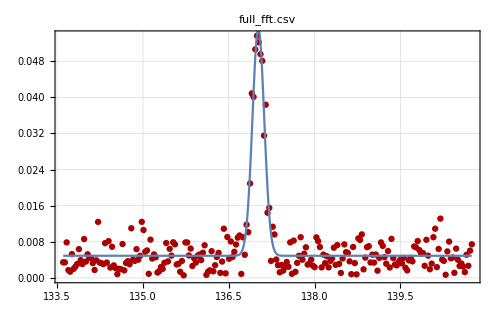
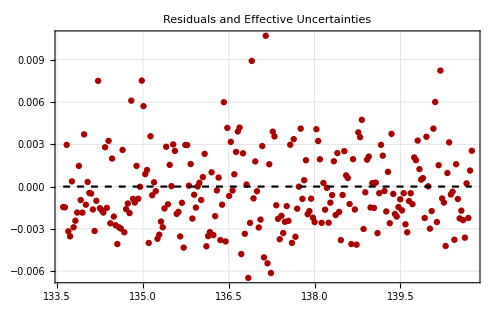
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
0.0503238 | c= 
0.00490238 | 
σ_y_max= 
0.00127453 | σ_c= 
0.000020003 | 
μ= 
137.016 | sigma= 
0.102836 | 
σ_μ= 
0.00275514 | σ_sigma= 
0.00294051 | Std. deviation= 
0.00255318

```mathematica
LinearDifferencePlot[]
```

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{134.984,139.002}

n= 131

104 points removed.

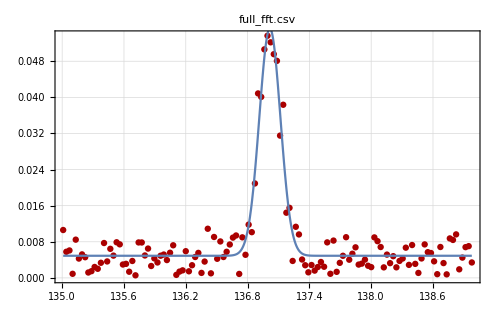
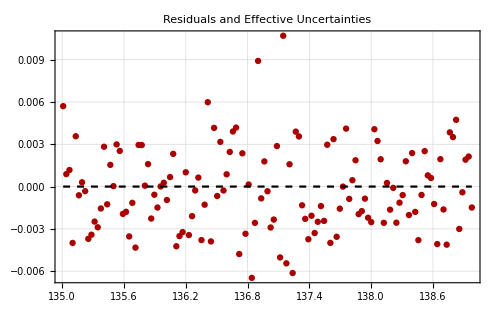
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
0.0503238 | c= 
0.00490238 | 
σ_y_max= 
0.00127453 | σ_c= 
0.000020003 | 
μ= 
137.016 | sigma= 
0.102836 | 
σ_μ= 
0.00275514 | σ_sigma= 
0.00294051 | Std. deviation= 
0.00255318

```mathematica
LinearDifferencePlot[]
```

```mathematica
1/(Sqrt[2] π sigma)
```

2.18872